```mathematica
ClearAll["Global`*"]
```

## c>0, q<0 , k>0,以下画的图均是函数的模

ϕ_7=ρ (1-(2 γ)/(γ+Cosh[2 √(-c/q) (-c t+x+ξ_0)]+ρ Sinh[2 √(-c/q) (-c t+x+ξ_0)]))生成

-Graphics3D-

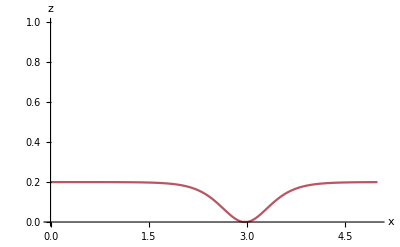

```mathematica
paraC=1;paraQ=-1;
paraX0 =-1;paraR =0.1;
paraT = 4;paraG =1;
setting1={ClippingStyle->None,
Exclusions->"Singularities",
ColorFunction-> "TemperatureMap",PlotPoints->60(* 60很顺滑*)
};

f[x_,t_]:=2 √(-c/q) ρ (1-(2 γ)/(γ+Cosh[4 √(-c/q) (-c t+x+Subscript[ξ, 0])]+ρ Sinh[4 √(-c/q) (-c t+x+Subscript[ξ, 0])]))/.{q->paraQ,c->paraC,Subscript[ξ, 0]->paraX0,ρ->paraR,γ->paraG,τ->paraT}//N;
Plot3D[Abs[f[x,t]],{x,-10,10},{t,0,3},Evaluate[setting1],PlotRange->{0,0.2},

AxesLabel->{"x","t","u_13"," "}]
Plot[Abs[f[x,2]],{x,0,5},AxesLabel->{x,z},ColorFunction-> "TemperatureMap",PlotRange->{0,1}]
```

-Graphics3D-

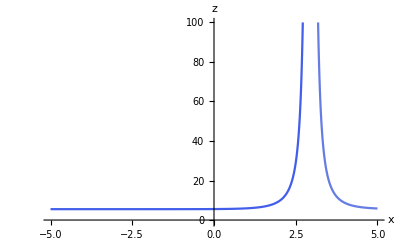

```mathematica
paraC=1;paraQ=-1;
paraX0 =-1;paraR =0.1;
paraT = 4;paraG =1;
setting1={ClippingStyle->None,
Exclusions->"Singularities",
ColorFunction-> "TemperatureMap"(*,PlotPoints->60(* 60很顺滑*)*)
};

f[x_,t_]:=-(ⅈ √c)/(2 √q)+c/(2 √(-c/q) q ρ (1-(2 γ)/(γ+Cosh[2 √(-c/q) (-c t+x+Subscript[ξ, 0])]+ρ Sinh[2 √(-c/q) (-c t+x+Subscript[ξ, 0])])))/.{q->paraQ,c->paraC,Subscript[ξ, 0]->paraX0,ρ->paraR,γ->paraG,τ->paraT}//N;
Plot3D[Abs[f[x,t]],{x,-10,10},{t,0,3},Evaluate[setting1],PlotRange->{-1,10},

AxesLabel->{"x","t","u_13"," "}]
Plot[Abs[f[x,2]],{x,-5,5},AxesLabel->{x,z},ColorFunction-> "TemperatureMap",PlotRange->{-1,100}]
```

-Graphics3D-

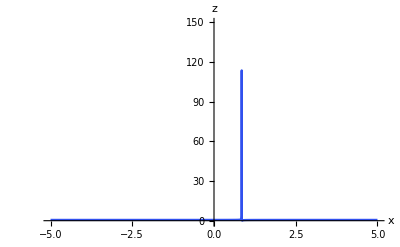

```mathematica
paraC=1;paraQ=-1;
paraX0 =0;paraR =0.01;
paraT = 4;paraG =4;
setting1={ClippingStyle->None,
Exclusions->"Singularities",
ColorFunction-> "TemperatureMap"(*,PlotPoints->60(* 60很顺滑*)*)
};

f[x_,t_]:=-(ⅈ √c)/(2 √q)+c/(2 √(-c/q) q ρ (1-(2 γ)/(γ+Cosh[2 √(-c/q) (-c t+x+Subscript[ξ, 0])]+ρ Sinh[2 √(-c/q) (-c t+x+Subscript[ξ, 0])])))/.{q->paraQ,c->paraC,Subscript[ξ, 0]->paraX0,ρ->5,γ->-0.5,τ->paraT}//N;
g[x_,t_]:=(2 c)/q-(2 c Coth[2 √(-c/q) (-c t+x)]^2)/q;
Plot3D[Abs[f[x,t]],{x,-10,10},{t,0,3},Evaluate[setting1],PlotRange->{-1,150},

AxesLabel->{"x","t","u_13"," "}]
Plot[Abs[f[x,1]],{x,-5,5},AxesLabel->{x,z},ColorFunction-> "TemperatureMap",PlotRange->{-1,150}]
```

```mathematica
Solve[1-(2 γ)/(γ+Cosh[2 √(-c/q) (-c t+x+Subscript[ξ, 0])]+ρ Sinh[2 √(-c/q) (-c t+x+Subscript[ξ, 0])])==0/.{q->paraQ,c->paraC,Subscript[ξ, 0]->paraX0,ρ->paraR,γ->paraG,τ->paraT,t->2},x]
```

Solve::ifun: Solve 正在使用反函数，因此可能无法找到某些解；请使用 Reduce 来获取完整的解信息.

{{x→1.91552},{x→1.91552+3.14159 ⅈ},{x→3.98415},{x→3.98415+3.14159 ⅈ}}

-Graphics3D-

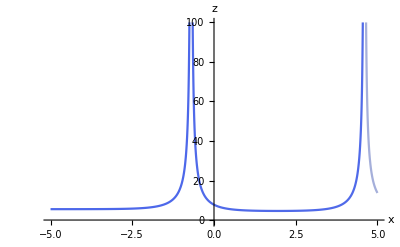

```mathematica
paraC=1;paraQ=-1;
paraX0 =0;paraR =0.1;
paraT = 4;paraG =100;
setting1={ClippingStyle->None,
Exclusions->"Singularities",
ColorFunction-> "TemperatureMap"(*,PlotPoints->60(* 60很顺滑*)*)
};

f[x_,t_]:=-(ⅈ √c)/(2 √q)+c/(2 √(-c/q) q ρ (1-(2 γ)/(γ+Cosh[2 √(-c/q) (-c t+x+Subscript[ξ, 0])]+ρ Sinh[2 √(-c/q) (-c t+x+Subscript[ξ, 0])])))/.{q->paraQ,c->paraC,Subscript[ξ, 0]->paraX0,ρ->paraR,γ->paraG,τ->paraT}//N;
g[x_,t_]:=(2 c)/q-(2 c Coth[2 √(-c/q) (-c t+x)]^2)/q;
Plot3D[Abs[f[x,t]],{x,-10,10},{t,0,3},Evaluate[setting1],

AxesLabel->{"x","t","u_13"," "}]
Plot[Abs[f[x,2]],{x,-5,5},AxesLabel->{x,z},ColorFunction-> "TemperatureMap",PlotRange->{-1,100}]
```

-Graphics3D-

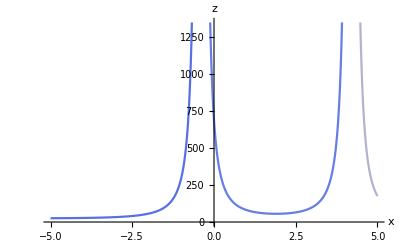

```mathematica
paraC=1;paraQ=-1;
paraX0 =0;paraR =0.1;
paraT = 4;paraG =5;
setting1={ClippingStyle->None,
Exclusions->"Singularities",
ColorFunction-> "TemperatureMap"(*,PlotPoints->60(* 60很顺滑*)*)
};

f[x_,t_]:=c/(2 q)-c/(4 q ρ^2 (1-(2 γ)/(γ+Cosh[√(-c/q) (-c t+x+Subscript[ξ, 0])]+ρ Sinh[√(-c/q) (-c t+x+Subscript[ξ, 0])]))^2)-(c ρ^2 (1-(2 γ)/(γ+Cosh[√(-c/q) (-c t+x+Subscript[ξ, 0])]+ρ Sinh[√(-c/q) (-c t+x+Subscript[ξ, 0])]))^2)/(4 q)/.{q->paraQ,c->paraC,Subscript[ξ, 0]->paraX0,ρ->paraR,γ->paraG,τ->paraT}//N;
g[x_,t_]:=(2 c)/q-(2 c Coth[2 √(-c/q) (-c t+x)]^2)/q;
Plot3D[Abs[f[x,t]],{x,-10,10},{t,0,3},Evaluate[setting1],

AxesLabel->{"x","t","u_13"," "}]
Plot[Abs[f[x,2]],{x,-5,5},AxesLabel->{x,z},ColorFunction-> "TemperatureMap"]
```

ϕ_3 生成的解，选择出来画图 ϕ_3=√k(Tanh[2 √k(z+ξ_0)]-I*ρ*Sech[2 √k(z+ξ_0)])

-Graphics3D-

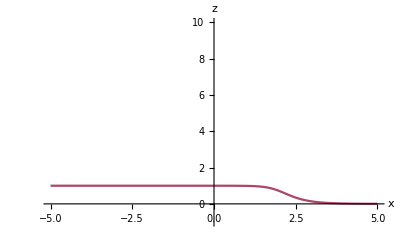

```mathematica
paraC=1;paraQ=-1;
paraX0 =0;paraR =-1;
paraT = 4;paraG =8;
setting1={ClippingStyle->None,
Exclusions->"Singularities",
ColorFunction-> "TemperatureMap",PlotPoints->70(* 60很顺滑*)
};

f[x_,t_]:=-(ⅈ √c)/(2 √q)-c/(2 √(-c/q) q (-ⅈ ρ Sech[2 √(-c/q) (-c t+x+Subscript[ξ, 0])]+Tanh[2 √(-c/q) (-c t+x+Subscript[ξ, 0])]))/.{q->paraQ,c->paraC,Subscript[ξ, 0]->paraX0,ρ->paraR,γ->paraG,τ->paraT}//N;
g[x_,t_]:=(2 c)/q-(2 c Coth[2 √(-c/q) (-c t+x)]^2)/q;
Plot3D[Abs[f[x,t]],{x,-5,5},{t,0,3},Evaluate[setting1],

AxesLabel->{"x","t","u_13"," "}]
Plot[Abs[f[x,2]],{x,-5,5},AxesLabel->{x,z},ColorFunction-> "TemperatureMap",PlotRange->{-1,10}]
```

-Graphics3D-

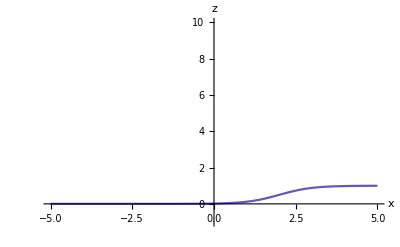

```mathematica
paraC=1;paraQ=-1;
paraX0 =0;paraR =-1;
paraT = 4;paraG =8;
setting1={ClippingStyle->None,
Exclusions->"Singularities",
ColorFunction-> "TemperatureMap"(*,PlotPoints->70(* 60很顺滑*)*)
};

f[x_,t_]:=-(ⅈ √c)/(2 √q)+c/(4 √(-c/q) q (-ⅈ ρ Sech[√(-c/q) (-c t+x+Subscript[ξ, 0])]+Tanh[√(-c/q) (-c t+x+Subscript[ξ, 0])]))-1/4 √(-c/q) (-ⅈ ρ Sech[√(-c/q) (-c t+x+Subscript[ξ, 0])]+Tanh[√(-c/q) (-c t+x+Subscript[ξ, 0])])/.{q->paraQ,c->paraC,Subscript[ξ, 0]->paraX0,ρ->paraR,γ->paraG,τ->paraT}//N;
g[x_,t_]:=(2 c)/q-(2 c Coth[2 √(-c/q) (-c t+x)]^2)/q;
Plot3D[Abs[f[x,t]],{x,-5,5},{t,0,3},Evaluate[setting1],

AxesLabel->{"x","t","u_13"," "}]
Plot[Abs[f[x,2]],{x,-5,5},AxesLabel->{x,z},ColorFunction-> "TemperatureMap",PlotRange->{-1,10}]
```

ϕ5= (-ρ √(k(γ^2+τ^2))+γ √k Cosh[2 √k(z+ξ_0)])/(γ*Sinh[2 √k(z+ξ_0)]+τ)生成

-Graphics3D-

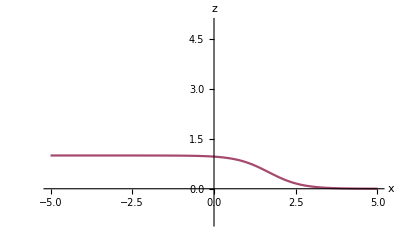

```mathematica
paraC=1;paraQ=-1;
paraX0 =0;paraR =-1;
paraT = 5;paraG =7;
setting1={ClippingStyle->None,
Exclusions->"Singularities",
ColorFunction-> "TemperatureMap",PlotPoints->70(* 60很顺滑*)
};

f[x_,t_]:=-(ⅈ √c)/(2 √q)-(c (τ+γ Sinh[2 √(-c/q) (-c t+x+Subscript[ξ, 0])]))/(2 q (-ρ √(-(c (γ^2+τ^2))/q)+√(-c/q) γ Cosh[2 √(-c/q) (-c t+x+Subscript[ξ, 0])]))/.{q->paraQ,c->paraC,Subscript[ξ, 0]->paraX0,ρ->paraR,γ->paraG,τ->paraT}//N;
g[x_,t_]:=(2 c)/q-(2 c Coth[2 √(-c/q) (-c t+x)]^2)/q;
Plot3D[Abs[f[x,t]],{x,-5,5},{t,0,3},Evaluate[setting1],

AxesLabel->{"x","t","u_13"," "}]
Plot[Abs[f[x,2]],{x,-5,5},AxesLabel->{x,z},ColorFunction-> "TemperatureMap",PlotRange->{-1,5}]
```

## c>0,q>0导致k<0

phi13=(-ρ*√(-k(γ^2-τ^2)-γ √-k Cos[2 √-k(z+ξ_0)]))/(γ*Sin[2 √-k(z+ξ_0)]+τ)生成周期解

-Graphics3D-

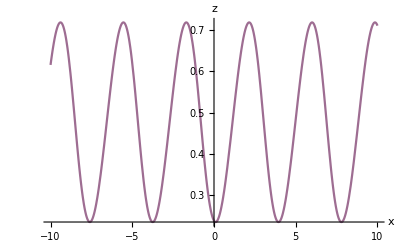

```mathematica
paraC=1;paraQ=6;
paraX0 =1;paraR =-1;
paraT = 4;paraG = 2;
setting1={ClippingStyle->None,
Exclusions->"Singularities",
ColorFunction-> "TemperatureMap",PlotPoints->60(* 60很顺滑*)
};

f[x_,t_]:=-(2 c (τ+γ Sin[4 √(c/q) (-c t+x+Subscript[ξ, 0])]))/(q ρ √((4 c (γ^2-τ^2))/q-2 √(c/q) γ Cos[4 √(c/q) (-c t+x+Subscript[ξ, 0])]))/.{q->paraQ,c->paraC,Subscript[ξ, 0]->paraX0,ρ->paraR,γ->paraG,τ->paraT}//N;
g[x_,t_]:=(2 c)/q-(2 c Coth[2 √(-c/q) (-c t+x)]^2)/q;
Plot3D[Abs[f[x,t]],{x,-10,10},{t,0,3},Evaluate[setting1],

AxesLabel->{"x","t","u_13"," "}]
Plot[Abs[f[x,2]],{x,-10,10},AxesLabel->{x,z},ColorFunction-> "TemperatureMap"]
```

-Graphics3D-

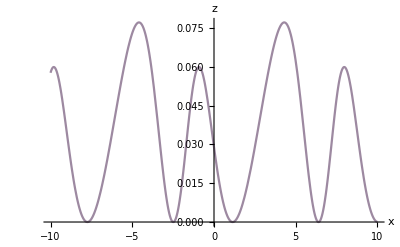

```mathematica
paraC=1;paraQ=2;
paraX0 =1;paraR =-1;
paraT = 4;paraG = 2;
setting1={ClippingStyle->None,
Exclusions->"Singularities",
ColorFunction-> "TemperatureMap",PlotPoints->60(* 60很顺滑*)
};

f[x_,t_]:=-(ⅈ √c)/(2 √q)-(ρ √((c (γ^2-τ^2))/(4 q)-1/2 √(c/q) γ Cos[√(c/q) (-c t+x+Subscript[ξ, 0])]))/(2 (τ+γ Sin[√(c/q) (-c t+x+Subscript[ξ, 0])]))+(c (τ+γ Sin[√(c/q) (-c t+x+Subscript[ξ, 0])]))/(8 q ρ √((c (γ^2-τ^2))/(4 q)-1/2 √(c/q) γ Cos[√(c/q) (-c t+x+Subscript[ξ, 0])]))/.{q->paraQ,c->paraC,Subscript[ξ, 0]->paraX0,ρ->paraR,γ->paraG,τ->paraT}//N;
g[x_,t_]:=(2 c)/q-(2 c Coth[2 √(-c/q) (-c t+x)]^2)/q;
Plot3D[Abs[f[x,t]],{x,-10,10},{t,0,3},Evaluate[setting1],

AxesLabel->{"x","t","u_13"," "}]
Plot[Abs[f[x,2]],{x,-10,10},AxesLabel->{x,z},ColorFunction-> "TemperatureMap"]
```

phi14=I*ρ*√-k(1-(2γ)/(γ+Cos[2 √-k(z+ξ_0)]+I*ρ*Sin[2 √-k(z+ξ_0)]))生成

-Graphics3D-

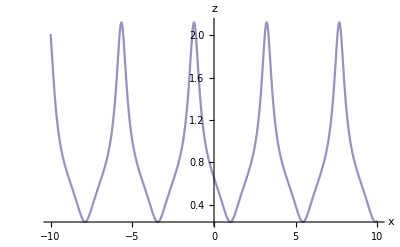

```mathematica
(*exprNeg=I*ρ*√-k(1-(2γ)/(γ+Cos[2 √-k(z+Subscript[ξ, 0])]+I*ρ*Sin[2 √-k(z+Subscript[ξ, 0])]));*)
paraC=1;paraQ=8;
paraX0 =1;paraR =2;
paraT = 4;paraG = 2;
setting1={ClippingStyle->None,
Exclusions->"Singularities",
ColorFunction-> "TemperatureMap",PlotPoints->60(* 60很顺滑*)
};

f[x_,t_]:=ⅈ √(c/q) ρ (1-(2 γ)/(γ+Cos[4 √(c/q) (-c t+x+Subscript[ξ, 0])]+ⅈ ρ Sin[4 √(c/q) (-c t+x+Subscript[ξ, 0])]))/.{q->paraQ,c->paraC,Subscript[ξ, 0]->paraX0,ρ->paraR,γ->paraG,τ->paraT}//N;
g[x_,t_]:=(2 c)/q-(2 c Coth[2 √(-c/q) (-c t+x)]^2)/q;
Plot3D[Abs[f[x,t]],{x,-10,10},{t,0,3},Evaluate[setting1],

AxesLabel->{"x","t","u_13"," "}]
Plot[Abs[f[x,2]],{x,-10,10},AxesLabel->{x,z},ColorFunction-> "TemperatureMap"]
```